# Compute the evolutionarily stable strategies (ESS)

Here, we compute the evolutionarily stable strategies (ESS) for the G-function defined by eqn. (5.1) in the paper. We encourage the reader to define its own G-function and follow the calculations in this script to calculate the corresponding ESS.
The ESS consists of a coalition of the population size x* and the trait value u*. We call x* the ecological equilibrium and u* the evolutionary equilibrium. The calculations and its results are also described in the supplementary.

## Define the G-function

```mathematica
carry[v_]:=Kmax*Exp[-v^2/sigmaK^2]
H[v_,m_]:=m*Exp[-v^2/sigmaH^2]
G[v_,u_,x_,m_]:=r*( 1-(x/carry[v]))-H[v,m]
```

## Compute the ecological equilibrium x*(u,m)

We obtain the ecological equilibrium by taking setting dx/dt=x G(v,u,x,m)=0. This either happens when x=0 or G=0. The case x=0 is trivial as the population is extinct and non-existing in this case. Thus, we look at the second case where G(v,u,x,m)=0. The ecological equilibrium is then calculated by

```mathematica
Solve[G[u,u,x,m]==0,x]
```

{{x→(ⅇ^(-u^2/sigmaH^2-u^2/sigmaK^2) Kmax (-m+ⅇ^(u^2/sigmaH^2) r))/r}}

Thus, we define the ecological equilibrium x*(u,m) by

```mathematica
xstar[u_,m_]:=(ⅇ^(-u^2/sigmaH^2-u^2/sigmaK^2) Kmax (-m+ⅇ^(u^2/sigmaH^2) r))/r
```

If x*(u,m)<0, this means that the population eventually goes extinct and x=0 is attractor. If x*(u,m)<0, the population will converge towards this population size. In the given example here, we see that x*(u,m)>0 for r > m.

## Compute evolutionary equilibrium u*(m)

The evolutionary equilibrium u*(m) is obtained by maximizing G with respect to v. Therefore, we first calculate the derivate of G after v.

```mathematica
dGdv[v_,u_,x_,m_]:=D[G[v,u,x,m],v]
Simplify[dGdv[v,u,x,m]]
```

(2 ⅇ^(-v^2/sigmaH^2) m v)/sigmaH^2-(2 ⅇ^(v^2/sigmaK^2) r v x)/(Kmax sigmaK^2)

We replace x by x*.

```mathematica
Simplify[(2 ⅇ^(-u^2/sigmaH^2) m u)/sigmaH^2-(2 ⅇ^(u^2/sigmaK^2) r u)/(Kmax sigmaK^2)(ⅇ^(-u^2/sigmaH^2-u^2/sigmaK^2) Kmax (-m+ⅇ^(u^2/sigmaH^2) r))/r]
```

(2 (-r+ⅇ^(-u^2/sigmaH^2) (m+(m sigmaK^2)/sigmaH^2)) u)/sigmaK^2

We set this expression to zero and solve for u.

```mathematica
Solve[(2 (-r+ⅇ^(-u^2/sigmaH^2) (m+(m sigmaK^2)/sigmaH^2)) u)/sigmaK^2==0,u]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{u→0},{u→-sigmaH √Log[(m sigmaH^2+m sigmaK^2)/(r sigmaH^2)]},{u→sigmaH √Log[(m sigmaH^2+m sigmaK^2)/(r sigmaH^2)]}}

In this case, we obtain three different solutions that correspond to a bifurcation as described in the paper and its supplementary.

```mathematica
ustar1[m_]:= sigmaH √Log[(m sigmaH^2+m sigmaK^2)/(r sigmaH^2)]
ustar2[m_]:= -sigmaH √Log[(m sigmaH^2+m sigmaK^2)/(r sigmaH^2)]
ustar0[m_]:=0
```

## Test stability of the equilibria

For completion, we want to make sure that u*(m) really maximizes G(v,u,x,m). Therefore, we calculate the second derivative after v:

```mathematica
d2Gdv2[v_,u_,x_,m_]:=D[dGdv[v,u,x,m],v]
Simplify[d2Gdv2[v,u,x,m]]
```

-(2 ⅇ^(v^2/sigmaK^2) r (sigmaK^2+2 v^2) x)/(Kmax sigmaK^4)

We discuss in the paper and its supplementary whether u* maximizes or minimizes G.

## Example plot

We make an example plot of the obtained equilibria.

```mathematica
sigmaH=2.0
sigmaK=3.0
r=2.0
```

2.

3.

2.

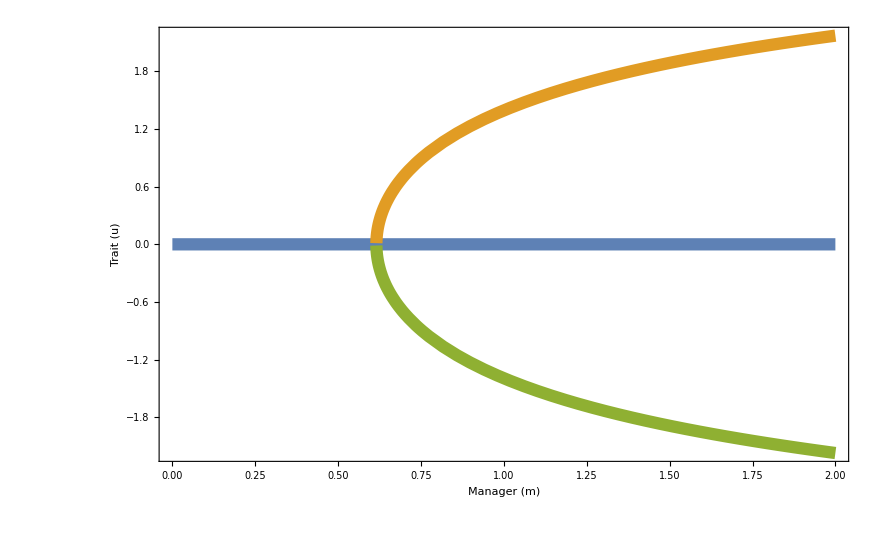

```mathematica
Plot[{ustar0[m],ustar1[m],ustar2[m]},{m,0,2},Frame->True,FrameLabel->{"Manager (m)","Trait (u)"},LabelStyle->"Subtitle",PlotStyle->Thickness[0.01]]
```